```mathematica
f[num_,size_,reg_,col_]:=Block[{c=RandomPoint[reg,num]},
For[r[1]=RandomReal@size;n=2,n≤num,n++,
r[n]=Max[Min@Append[Norm[c[[n]]-c[[#]]]-r[#]&/@Range[n-1],RandomReal@size],0.05];
];
Show[Graphics[{RandomColor[Hue[col,NormalDistribution[.6,.2],NormalDistribution[.6,.07]]],Disk[c[[#]],r[#]]}]&/@Select[Range[num],r[#]≠0.05&&RegionWithin[reg,Disk[c[[#]],r[#]]]&],ImageSize-> 500]
];
```

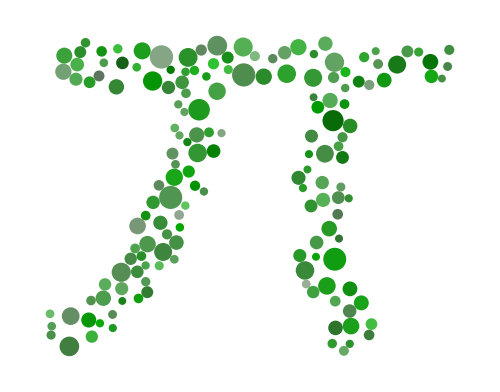

/Users/apple/Desktop/Pi.jpg

```mathematica
reg1=DiscretizeGraphics[Text[Style["π",Bold]],_Text,MaxCellMeasure->0.1];
f[2000,{0.05,0.15},reg1,1/3]
(*N(.6,.2),N(.8,.07)*)
Export["/Users/apple/Desktop/Pi.jpg",%,ImageResolution->500]
```

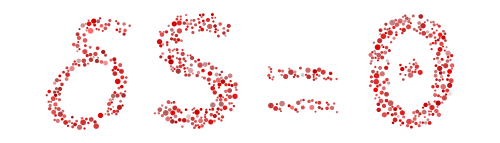

/Users/apple/Desktop/deltaS=0.jpg

```mathematica
reg2=DiscretizeGraphics[Text[Style["δS=0",Bold]],_Text,MaxCellMeasure->0.1];
f[2000,{0.05,0.15},reg2,1]
Export["/Users/apple/Desktop/deltaS=0.jpg",%,ImageResolution->500]
```